```mathematica
numberOfColors =2;
range = 2;
ruleNumber=RandomInteger[numberOfColors^(numberOfColors^(2*range+1))]
initialCondition = RandomInteger[{0,1},20]
numberOfSteps = 25;
evolution = CellularAutomaton[{ruleNumber,numberOfColors,range},initialCondition,numberOfSteps];
ArrayPlot@evolution
```

463828577

{0,0,1,1,1,1,1,1,1,1,0,0,0,1,1,0,1,1,0,1}

-Graphics-

Compare top approach with normal to check understanding

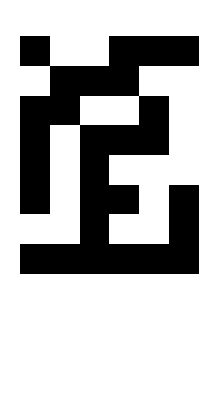

{1,1,0,0,0,1,0,0,1,0}

```mathematica
evolution = CellularAutomaton[ruleNumber,initialCondition,numberOfSteps];
ArrayPlot@evolution
```

testing higher dimensionality, 2D in specific.

```mathematica
initialCondition = RandomInteger[{0,1},{3,3}]
numberOfSteps = 3;
```

{{1,1,1},{1,1,0},{1,1,0}}

```mathematica
evolution = CellularAutomaton[{ruleNumber,numberOfColors,{range,range}},initialCondition,numberOfSteps];
Column@evolution
```

{{1,1,1},{1,1,0},{1,1,0}}
{{0,0,0},{0,0,0},{0,0,0}}
{{1,1,1},{1,1,1},{1,1,1}}
{{0,0,0},{0,0,0},{0,0,0}}